```mathematica
Clear[x,y,z,s,xp,yp]
l={{-xp,s/2,0},{-s/2,-yp,0},{xp,-s/2,0},{s/2,yp,0}};
dl={{-1,0,0},{0,-1,0},{1,0,0},{0,1,0}};
R1={x,y,z}-l[[1]]
R2={x,y,z}-l[[2]]
R3={x,y,z}-l[[3]]
R4={x,y,z}-l[[4]]
mod1=Sqrt[R1.R1];
mod2=Sqrt[R2.R2];
mod3=Sqrt[R3.R3];
mod4=Sqrt[R4.R4];
c1=Cross[dl[[1]],R1];
c2=Cross[dl[[2]],R2];
c3=Cross[dl[[3]],R3];
c4=Cross[dl[[4]],R4];
inte1=c1/(mod1^3);
inte2=c2/(mod2^3);
inte3=c3/(mod3^3);
inte4=c4/(mod4^3);
intex=inte1[[1]]+inte2[[1]]+inte3[[1]]+inte4[[1]]
intey=inte1[[2]]+inte2[[2]]+inte3[[2]]+inte4[[2]]
intez=inte1[[3]]+inte2[[3]]+inte3[[3]]+inte4[[3]]
```

{x+xp,-s/2+y,z}

{s/2+x,y+yp,z}

{x-xp,s/2+y,z}

{-s/2+x,y-yp,z}

z/(((-s/2+x)^2+(y-yp)^2+z^2)^(3/2))-z/(((s/2+x)^2+(y+yp)^2+z^2)^(3/2))

z/(((x+xp)^2+(-s/2+y)^2+z^2)^(3/2))-z/(((x-xp)^2+(s/2+y)^2+z^2)^(3/2))

(s/2-y)/(((x+xp)^2+(-s/2+y)^2+z^2)^(3/2))+(s/2+y)/(((x-xp)^2+(s/2+y)^2+z^2)^(3/2))+(s/2-x)/(((-s/2+x)^2+(y-yp)^2+z^2)^(3/2))+(s/2+x)/(((s/2+x)^2+(y+yp)^2+z^2)^(3/2))

```mathematica
(*Clear[x,y,z,s]*)
{xp,yp}:={ep,ep};
Bz=Assuming[0.03>s>0&&z>0&&-2s<x<2s&&-2s<y<2s,Integrate[intez,{ep,-s/2,s/2}]]
```

(√2 (s-2 y) (2 x (1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))-1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))+1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))))/((s-2 y)^2+4 z^2)+(√2 (s-2 x) (2 y (1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))-1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))+1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))))/((s-2 x)^2+4 z^2)+(2 √2 (s/2+x) (2 y (-1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))))/((s+2 x)^2+4 z^2)+(2 √2 (s/2+y) (2 x (-1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))))/((s+2 y)^2+4 z^2)

```mathematica
(*Clear[x,y,z,s]*)
Bx=Assuming[0.03>s>0&&0.02>z>0&&-2s<x<2s&&-2s<y<2s,Integrate[intex,{ep,-s/2,s/2}]]
```

(2 √2 z (2 y (1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))-1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))+1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))))/((s-2 x)^2+4 z^2)-(2 √2 z (2 y (-1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))))/((s+2 x)^2+4 z^2)

```mathematica
(*Clear[x,y,z,s]*)
By=Assuming[0.03>s>0&&0.02>z>0&&-2s<y<2s&&-2s<x<2s,Integrate[intey,{ep,-s/2,s/2}]]
```

(2 √2 z (2 x (1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))-1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (x-y)+2 (x^2+y^2+z^2)))+1/(√(s^2-2 s (x+y)+2 (x^2+y^2+z^2))))))/((s-2 y)^2+4 z^2)-(2 √2 z (2 x (-1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))+s (1/(√(s^2+2 s (-x+y)+2 (x^2+y^2+z^2)))+1/(√(s^2+2 s (x+y)+2 (x^2+y^2+z^2))))))/((s+2 y)^2+4 z^2)

```mathematica
z=2*10^(-3);
s=5.97*10^(-3);
Plot3D[(Sqrt[((Norm[0.1*Bx]^2 )+(Norm[0.1*Bz]^2)+(Norm[0.1*By]^2))]),{x,-0.010,0.010},{y,-0.010,0.010},ColorFunction->Function[{x,y,z},Hue[0.65(1-z)]],Mesh->40,AxesLabel->{"x-coordinate (m)","y-coordinate (m)","B field
 (μT)/A"}]
```

-Graphics3D-

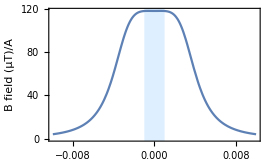

```mathematica
y=0;
Plot[(Sqrt[((Norm[0.1Bx]^2 )+(Norm[0.1Bz]^2))]),{x,-0.01,0.01},Prolog->{LightBlue,Rectangle[{-0.0010,-10},{0.0010,10000}]},Frame->True,FrameLabel->{"x-coordinate (m)","B field (μT)/A"}]
```

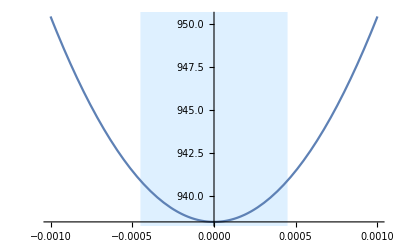

```mathematica
x=0;
Plot[(Sqrt[((Norm[By]^2 )+(Norm[Bz]^2))]),{y,-0.001,0.001},Prolog->{LightBlue,Rectangle[{-0.00045,0.000},{0.00045,10000}]}]
```

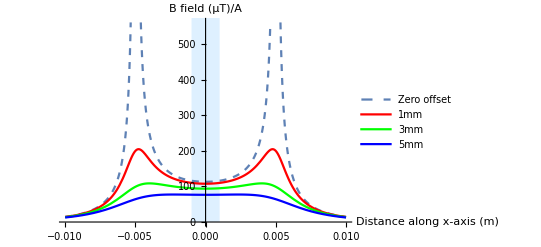

```mathematica
z=0*10^(-3);
zero=Plot[ ( Sqrt[(Norm[0.1Bx]^2) + (Norm[0.1Bz]^2)]),{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","B field (μT)/A"},AxesLabel->StandardForm,PlotStyle->Dashed,PlotLegends->{"Zero offset"}];
z=1*10^(-3);
one=Plot[ ( Sqrt[(Norm[0.1Bx]^2) + (Norm[0.1Bz]^2)]),{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm,PlotStyle->Red,PlotLegends->{"1mm"}];
z=2*10^(-3);
two=Plot[ ( Sqrt[(Norm[0.1Bx]^2) + (Norm[0.1Bz]^2)]),{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm, PlotStyle->Green,PlotLegends->{"3mm"}];
z=3*10^(-3);
three =Plot[ ( Sqrt[(Norm[0.1Bx]^2) + (Norm[0.1Bz]^2)]),{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm,PlotStyle->Blue,PlotLegends->{"5mm"}];
Show[zero,one,two,three,Prolog->{LightBlue,Rectangle[{-0.001,0.000},{0.001,5000}]}]
```

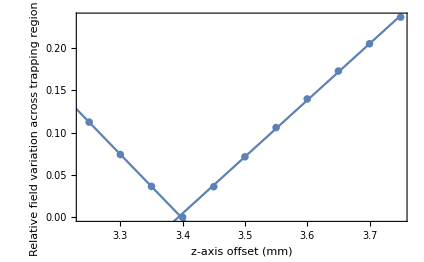

{0.01,a→3.39562}

```mathematica
Clear[x,y,z,s]
y=0;
s=10*10^(-3);
z=3.5*10^(-3);
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1*10^(-3);

z=(eyeball - 5*it);
x = 0*10^(-3);
midField =Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel1=Abs[(edgeField-midField)/midField]*100;

z=(eyeball - 4*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel2=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel3=Abs[(edgeField-midField)/midField]*100;

z=(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel4=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel5=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel6=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel7=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel8=Abs[(edgeField-midField)/midField]*100;

z =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel9=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel10=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel11=Abs[(edgeField-midField)/midField]*100;

z1=1000(eyeball - 5*it);
z2 =1000(eyeball - 4*it);
z3=1000(eyeball - 3*it);
z4=1000(eyeball - 2*it);
z5=1000(eyeball - 1*it);
z6=1000(eyeball - 0*it);
z7=1000(eyeball + 1*it);
z8=1000(eyeball + 2*it);
z9=1000(eyeball + 3*it);
z10=1000(eyeball + 4*it);
z11=1000(eyeball + 5*it);

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;3]],{1,a,a},a];
lineincrease=Fit[relfield[[5;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"},Frame->True,FrameLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5={ N[s],Zopt[[1,1]]}
```

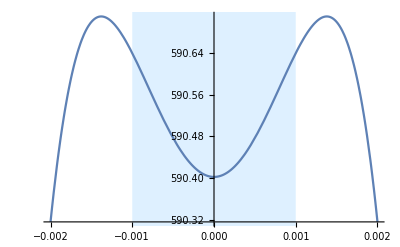

```mathematica
s=12*10^(-3);
z=4*10^(-3);
y=0;
Plot[(Sqrt[((Norm[Bx]^2 )+(Norm[Bz]^2))]),{x,-0.002,0.002},Prolog->{LightBlue,Rectangle[{-0.0010,0.000},{0.0010,10000}]}]
```

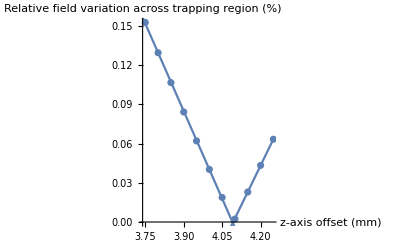

{0.012,a→4.09149}

```mathematica
z=4*10^(-3);
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1*10^(-3);

z=(eyeball - 5*it);
x = 0*10^(-3);
midField =Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel1=Abs[(edgeField-midField)/midField]*100;

z=(eyeball - 4*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel2=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel3=Abs[(edgeField-midField)/midField]*100;

z=(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel4=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel5=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel6=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel7=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel8=Abs[(edgeField-midField)/midField]*100;

z =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel9=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel10=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel11=Abs[(edgeField-midField)/midField]*100;

z1=1000(eyeball - 5*it);
z2 =1000(eyeball - 4*it);
z3=1000(eyeball - 3*it);
z4=1000(eyeball - 2*it);
z5=1000(eyeball - 1*it);
z6=1000(eyeball - 0*it);
z7=1000(eyeball + 1*it);
z8=1000(eyeball + 2*it);
z9=1000(eyeball + 3*it);
z10=1000(eyeball + 4*it);
z11=1000(eyeball + 5*it);

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;7]],{1,a,a},a];
lineincrease=Fit[relfield[[9;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5={ N[s],Zopt[[1,1]]}
```

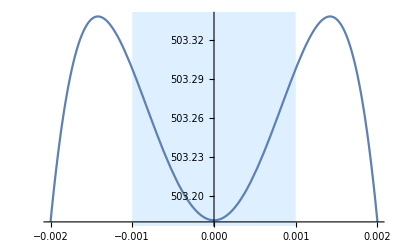

```mathematica
s=14*10^(-3);
z=4.7*10^(-3);
y=0;
Plot[(Sqrt[((Norm[Bx]^2 )+(Norm[Bz]^2))]),{x,-0.002,0.002},Prolog->{LightBlue,Rectangle[{-0.0010,0.000},{0.0010,10000}]}]
```

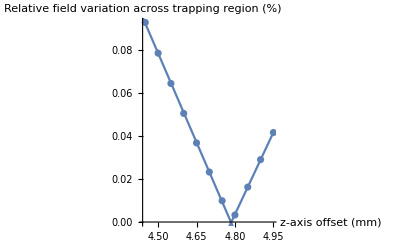

{0.014,a→4.78493}

```mathematica
z=4.7*10^(-3);
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1*10^(-3);

z=(eyeball - 5*it);
x = 0*10^(-3);
midField =Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel1=Abs[(edgeField-midField)/midField]*100;

z=(eyeball - 4*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel2=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel3=Abs[(edgeField-midField)/midField]*100;

z=(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel4=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel5=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel6=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel7=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel8=Abs[(edgeField-midField)/midField]*100;

z =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel9=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel10=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel11=Abs[(edgeField-midField)/midField]*100;

z1=1000(eyeball - 5*it);
z2 =1000(eyeball - 4*it);
z3=1000(eyeball - 3*it);
z4=1000(eyeball - 2*it);
z5=1000(eyeball - 1*it);
z6=1000(eyeball - 0*it);
z7=1000(eyeball + 1*it);
z8=1000(eyeball + 2*it);
z9=1000(eyeball + 3*it);
z10=1000(eyeball + 4*it);
z11=1000(eyeball + 5*it);

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;7]],{1,a,a},a];
lineincrease=Fit[relfield[[9;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5={ N[s],Zopt[[1,1]]}
```

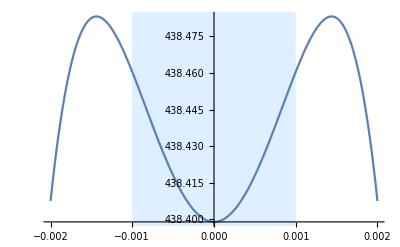

```mathematica
s=16*10^(-3);
z=5.4*10^(-3);
y=0;
Plot[(Sqrt[((Norm[Bx]^2 )+(Norm[Bz]^2))]),{x,-0.002,0.002},Prolog->{LightBlue,Rectangle[{-0.0010,0.000},{0.0010,10000}]}]
```

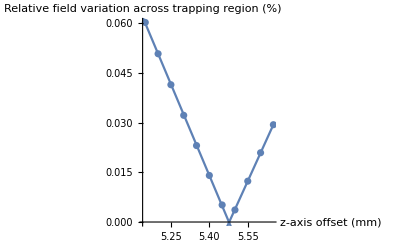

{0.016,a→5.47701}

```mathematica
z=5.4*10^(-3);
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1*10^(-3);

z=(eyeball - 5*it);
x = 0*10^(-3);
midField =Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel1=Abs[(edgeField-midField)/midField]*100;

z=(eyeball - 4*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel2=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel3=Abs[(edgeField-midField)/midField]*100;

z=(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel4=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel5=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel6=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel7=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel8=Abs[(edgeField-midField)/midField]*100;

z =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel9=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel10=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel11=Abs[(edgeField-midField)/midField]*100;

z1=1000(eyeball - 5*it);
z2 =1000(eyeball - 4*it);
z3=1000(eyeball - 3*it);
z4=1000(eyeball - 2*it);
z5=1000(eyeball - 1*it);
z6=1000(eyeball - 0*it);
z7=1000(eyeball + 1*it);
z8=1000(eyeball + 2*it);
z9=1000(eyeball + 3*it);
z10=1000(eyeball + 4*it);
z11=1000(eyeball + 5*it);

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;7]],{1,a,a},a];
lineincrease=Fit[relfield[[9;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5={ N[s],Zopt[[1,1]]}
```

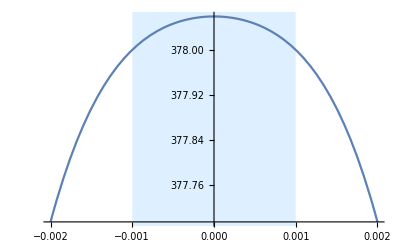

```mathematica
s=18*10^(-3);
z=6.3*10^(-3);
y=0;
Plot[(Sqrt[((Norm[Bx]^2 )+(Norm[Bz]^2))]),{x,-0.002,0.002},Prolog->{LightBlue,Rectangle[{-0.0010,0.000},{0.0010,10000}]}]
```

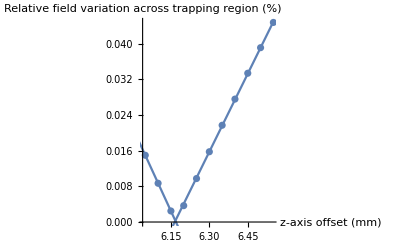

{0.018,a→6.16743}

```mathematica
z=6.3*10^(-3);
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1*10^(-3);

z=(eyeball - 5*it);
x = 0*10^(-3);
midField =Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel1=Abs[(edgeField-midField)/midField]*100;

z=(eyeball - 4*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel2=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel3=Abs[(edgeField-midField)/midField]*100;

z=(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel4=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel5=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel6=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel7=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel8=Abs[(edgeField-midField)/midField]*100;

z =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel9=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel10=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel11=Abs[(edgeField-midField)/midField]*100;

z1=1000(eyeball - 5*it);
z2 =1000(eyeball - 4*it);
z3=1000(eyeball - 3*it);
z4=1000(eyeball - 2*it);
z5=1000(eyeball - 1*it);
z6=1000(eyeball - 0*it);
z7=1000(eyeball + 1*it);
z8=1000(eyeball + 2*it);
z9=1000(eyeball + 3*it);
z10=1000(eyeball + 4*it);
z11=1000(eyeball + 5*it);

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;3]],{1,a,a},a];
lineincrease=Fit[relfield[[5;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5={ N[s],Zopt[[1,1]]}
```

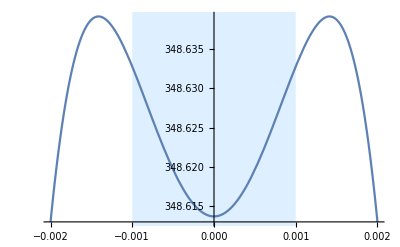

```mathematica
s=20*10^(-3);
z=6.8*10^(-3);
y=0;
Plot[(Sqrt[((Norm[Bx]^2 )+(Norm[Bz]^2))]),{x,-0.002,0.002},Prolog->{LightBlue,Rectangle[{-0.0010,0.000},{0.0010,10000}]}]
```

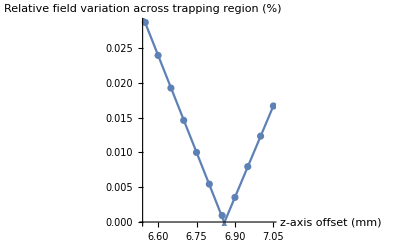

{0.02,a→6.85854}

```mathematica
z=6.8*10^(-3);
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1*10^(-3);

z=(eyeball - 5*it);
x = 0*10^(-3);
midField =Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel1=Abs[(edgeField-midField)/midField]*100;

z=(eyeball - 4*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel2=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel3=Abs[(edgeField-midField)/midField]*100;

z=(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel4=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel5=Abs[(edgeField-midField)/midField]*100;

z =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel6=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel7=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel8=Abs[(edgeField-midField)/midField]*100;

z =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz];
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel9=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel10=Abs[(edgeField-midField)/midField]*100;

z =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz];
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)]);
rel11=Abs[(edgeField-midField)/midField]*100;

z1=1000(eyeball - 5*it);
z2 =1000(eyeball - 4*it);
z3=1000(eyeball - 3*it);
z4=1000(eyeball - 2*it);
z5=1000(eyeball - 1*it);
z6=1000(eyeball - 0*it);
z7=1000(eyeball + 1*it);
z8=1000(eyeball + 2*it);
z9=1000(eyeball + 3*it);
z10=1000(eyeball + 4*it);
z11=1000(eyeball + 5*it);

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;6]],{1,a,a},a];
lineincrease=Fit[relfield[[8;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5={ N[s],Zopt[[1,1]]}
```

-0.0639383+0.346207 r

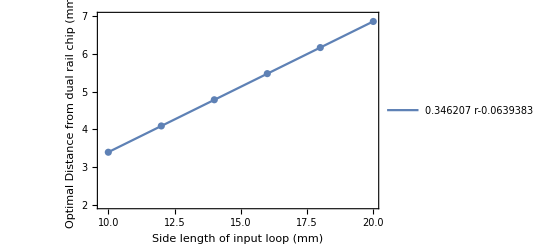

```mathematica
OptimiseData={{10,3.3956183058240548},{12,4.091490156046983},{14,4.784934706531775},{16,5.477012679532004},{18,6.167427280771507},{20,6.85854233679865}};
OptimisationFunc=Fit[OptimiseData,{1,r,r},r]

Show[ListPlot[OptimiseData,AxesLabel->{"Side length of input loop (mm)","Optimal Distance from dual rail chip (mm)"},Frame->True,FrameLabel->{"Side length of input loop (mm)","Optimal Distance from dual rail chip (mm)"},PlotRange->{2,7}],Plot[OptimisationFunc,{r,10,20},PlotLegends->{OptimisationFunc}]]
```